Lu 167 Energies

## x from Nucl data taken as a known value (30 KeV)

```mathematica
d1={2.4578516994627413,2.9471060403528915,3.481426834105881,4.060832832059294,4.68533866600645,5.354955946188581,6.069694020614097,6.829560513049348,7.634561712233382,8.484702858661556,9.379988359363105,10.320421951121162,11.3060068261636,12.336745730126234,13.412641039250044,14.533694821831663,15.699908887595821};
d2={4.05027961242229,4.666436437227856,5.3275055462393786,6.033520495543726,6.784508890703831,7.580493717697189,8.421494320833501,9.307527134496597,10.238606239593905,11.214743792854291,12.235950362354636,13.302235192853729,14.413606417868634,15.570071230842602};
```

```mathematica
tsd1={2249.7,2720.5,3225.6,3786.5,4393.3,5048.0,5749.8,6501.5,7300.4,8154.9,9080.9,10040,11056,12132,13267,14459,15706};
tsd1=tsd1/1000;
tsd1=tsd1+0.030;
tsd2={3945.6,4492.6,5097.6,5755.7,6466.7,7231.8,8047.8,8917.8,9841,10817,11849,12933,14082,15282};
tsd2=tsd2/1000;
tsd2=tsd2+0.030;
```

```mathematica
p1=Plot[Table[tsd1[[y]],{y,17}],{x,0,0.4},PlotStyle->Directive[Black,Thickness[0.004]]];
p2=Plot[Table[tsd2[[y]],{y,14}],{x,2,2.4},PlotStyle->Directive[Black,Thickness[0.004]]];
s1=Plot[Table[d1[[y]],{y,17}],{x,0.8,1.2},PlotStyle->Directive[Black,Thickness[0.005]]];
s2=Plot[Table[d2[[y]],{y,14}],{x,2.8,3.2},PlotStyle->Directive[Black,Thickness[0.005]]];
```

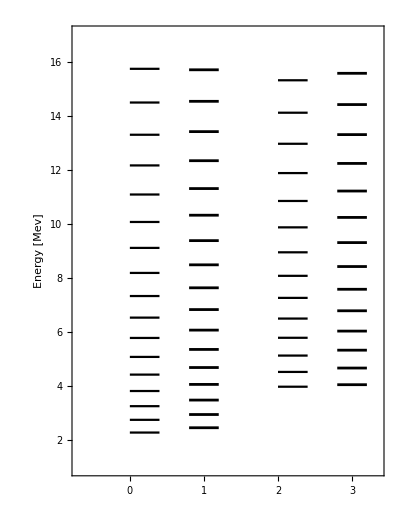

```mathematica
Show[{p1,s1,s2,p2},Axes->False,PlotRange->{{-0.7,3.35},{1,17}},Frame-> True,Axes->False,FrameStyle->{{White},{Normal},{White},{Normal}},FrameLabel->{{"Energy [Mev]",""},{"",""}},LabelStyle->{Black,Bold,FontFamily->"Times New Roman",FontSize-> 17},FrameTicksStyle->{{{Black},{Black}},{}},FrameTicks->{Automatic,{2,4,6,8,10,12,14,16}},AspectRatio->1.3]
```